```mathematica
findRepetition[rule_, init_]:=
NestWhileList[
CellularAutomaton[rule, #]&,
init, UnsameQ, All
]
```

```mathematica
findPeriod[states_]:=
Length[states] - First[FirstPosition[states,Last@states]]
```

```mathematica
allStates=Table[Function[states, {Length@states, 1+Length@states - First@FirstPosition[states, CellularAutomaton[110, Last@states]]}]@Module[{states = CreateDataStructure["HashSet"], init = CenterArray[1, i]},
states["Insert", FromDigits[init, 2]];
NestWhileList[
With[{next=CellularAutomaton[110, #]},
states["Insert", FromDigits[next,2]];
next]&,
init,
!states["MemberQ", FromDigits[CellularAutomaton[110, #], 2]]&
]],{i,1,100}]
```

{{2,1},{3,1},{4,1},{4,2},{6,1},{11,9},{18,14},{20,16},{9,7},{29,25},{123,110},{15,9},{367,351},{111,91},{307,295},{81,32},{41,7},{108,27},{336,285},{83,30},{676,630},{105,44},{1120,1058},{183,36},{339,250},{249,7},{508,405},{1754,1652},{1179,1044},{148,60},{98,7},{212,64},{647,495},{158,51},{1147,1050},{200,72},{4595,4403},{289,76},{562,390},{456,60},{221,7},{872,630},{1759,1548},{450,88},{385,7},{224,7},{1209,705},{528,96},{1678,1470},{250,100},{1487,765},{473,195},{8236,8109},{204,7},{1108,825},{390,7},{2434,2052},{785,116},{370,7},{20306,19560},{1362,915},{167,7},{2503,1890},{608,128},{1178,975},{275,132},{902,670},{266,136},{2157,2001},{449,7},{18708,17963},{312,144},{22482,22119},{494,148},{1649,1125},{2192,1596},{1519,1155},{1469,156},{239,7},{1116,160},{2002,1215},{1610,1230},{1475,1245},{1128,630},{26878,26605},{305,129},{988,7},{596,176},{42043,41830},{1573,1350},{3192,2730},{24462,24265},{223,7},{1058,188},{2253,1425},{545,144},{11718,11349},{1760,1470},{4132,3564},{1248,900}}

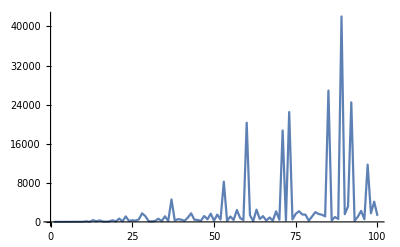

```mathematica
ListLinePlot[First/@allStates, PlotRange->All]
```

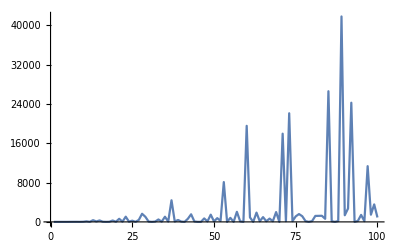

```mathematica
ListLinePlot[Last/@allStates,PlotRange->All]
```

```mathematica
First/@allStates
```

{2,3,4,4,6,11,18,20,9,29,123,15,367,111,307,81,41,108,336,83,676,105,1120,183,339,249,508,1754,1179,148,98,212,647,158,1147,200,4595,289,562,456,221,872,1759,450,385,224,1209,528,1678,250,1487,473,8236,204,1108,390,2434,785,370,20306,1362,167,2503,608,1178,275,902,266,2157,449,18708,312,22482,494,1649,2192,1519,1469,239,1116,2002,1610,1475,1128,26878,305,988,596,42043,1573,3192,24462,223,1058,2253,545,11718,1760,4132,1248}

```mathematica
Last/@allStates
```

{1,1,1,2,1,9,14,16,7,25,110,9,351,91,295,32,7,27,285,30,630,44,1058,36,250,7,405,1652,1044,60,7,64,495,51,1050,72,4403,76,390,60,7,630,1548,88,7,7,705,96,1470,100,765,195,8109,7,825,7,2052,116,7,19560,915,7,1890,128,975,132,670,136,2001,7,17963,144,22119,148,1125,1596,1155,156,7,160,1215,1230,1245,630,26605,129,7,176,41830,1350,2730,24265,7,188,1425,144,11349,1470,3564,900}

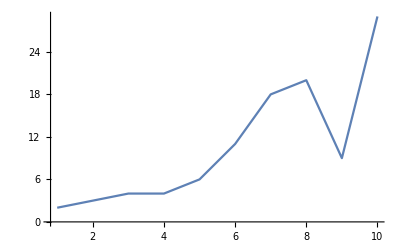

```mathematica
ListLinePlot[{2,3,4,4,6,11,18,20,9,29,123,15,367,111,307,81,41,108,336,83,676,105,1120,183,339,249,508,1754,1179,148,98,212,647,158,1147,200,4595,289,562,456,221,872,1759,450,385,224,1209,528,1678,250,1487,473,8236,204,1108,390,2434,785,370,20306,1362,167,2503,608,1178,275,902,266,2157,449,18708,312,22482,494,1649,2192,1519,1469,239,1116,2002,1610,1475,1128,26878,305,988,596,42043,1573,3192,24462,223,1058,2253,545,11718,1760,4132,1248}[[;;10]],PlotRange->All]
```

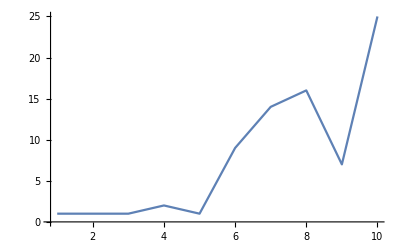

```mathematica
ListLinePlot[{1,1,1,2,1,9,14,16,7,25,110,9,351,91,295,32,7,27,285,30,630,44,1058,36,250,7,405,1652,1044,60,7,64,495,51,1050,72,4403,76,390,60,7,630,1548,88,7,7,705,96,1470,100,765,195,8109,7,825,7,2052,116,7,19560,915,7,1890,128,975,132,670,136,2001,7,17963,144,22119,148,1125,1596,1155,156,7,160,1215,1230,1245,630,26605,129,7,176,41830,1350,2730,24265,7,188,1425,144,11349,1470,3564,900}[[;;10]],PlotRange->All]
```

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},10000], ImageSize->{1000,10000}]
```